```mathematica
Entropy of a two-level system
```

Consider a two-level system with energies E=N_1(-ϵ)+N_2(ϵ)=-ϵ(N_1-N_2) and the number of particles N=N_1+N_2, hence the number of microscopic states is W(E,N)=(N!)/(N_1!N_2!). Substituting the number of microscopic states W(E,N) into the Boltzmann’s entropy formula S=k_B logW and simplifying, it gives S=-1×1/2 N k_B{(1-E/(N ϵ))log(1-E/(N ϵ))+(1+E/(N ϵ))log(1+E/(N ϵ))}+N k_B log2. E/(N ϵ) can be regarded as an argument x, and S/(N k_B) can be regarded as a dependent variable f(x). This paper aims to visualize the function.

0.562335

1/2 (Log[1-x]-Log[1+x])

0.549306

{{b→0.836988}}

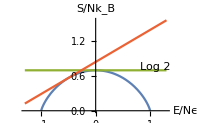

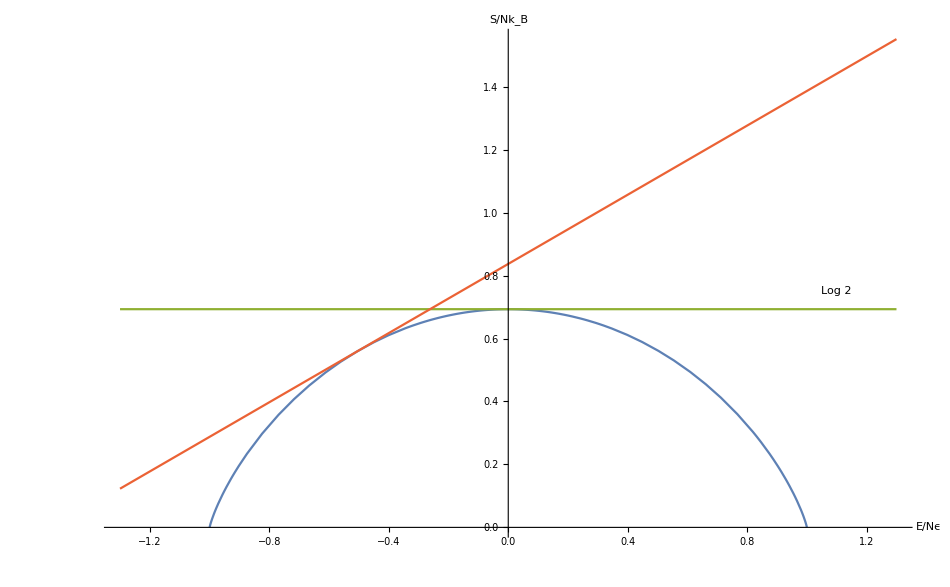

```mathematica
-1/2((1-(-0.5))×Log[(1-(-0.5))]+(1+(-0.5))×Log[(1+(-0.5))])+Log[2](*f(-0.5)*)
D[-1/2((1-x)×Log[(1-x)]+(1+x)×Log[(1+x)])+Log[2],x](*f'(x)=(df(x))/dx*)
1/2 (Log[1-(-0.5)]-Log[1+(-0.5)])(*Slope k=f'(-0.5)*)
Solve[-1/2((1-(-0.5))×Log[(1-(-0.5))]+(1+(-0.5))×Log[(1+(-0.5))])+Log[2]==(1/2 (Log[1-(-0.5)]-Log[1+(-0.5)]))*(-0.5)+b,b](*Solve f(-0.5)=f'(-0.5)×(-0.5)+b to get b*)
Plot[{{-1/2((1-x)×Log[(1-x)]+(1+x)×Log[(1+x)])+Log[2],1<=x<=2},
{Log[2]},
{(1/2 (Log[1-(-0.5)]-Log[1+(-0.5)]))x+0.8369882167858357}},{x,-1.3,1.3},
PlotRange->Full,AxesLabel->{"E/Nϵ","S/Nk_B"},
Epilog->Text["Log 2",{1.1,0.75}],
PlotLegends->{"S","S0.836988","log 2"},ImageSize->200]
```